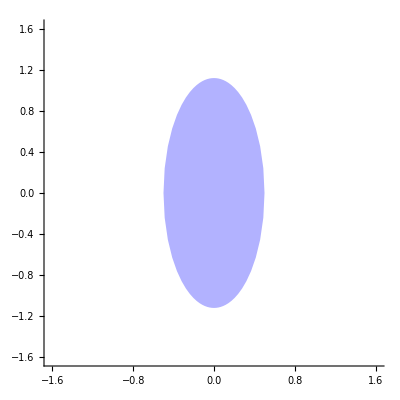

```mathematica
NumericalRangeVisual[I*{
{-1, 1},
{0, 1}
}]
```

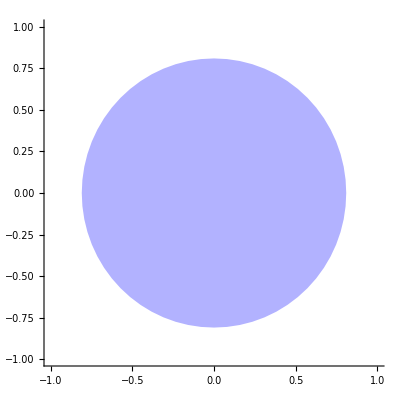

```mathematica
NumericalRangeVisual[
{
{0, 0, 0, 0},
{1, 0, 0, 0},
{0, 1, 0, 0},
{0, 0, 1, 0}
}
]
```

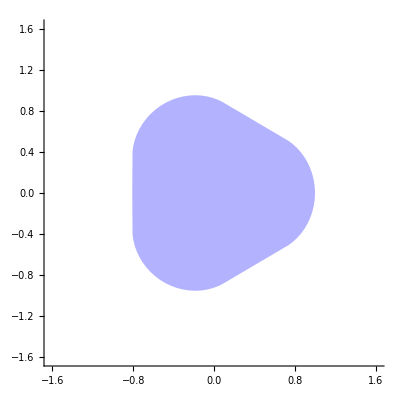

```mathematica
NumericalRangeVisual[
{
{0, 1, 0, 0, 1},
{0, 0, 1, 0, 0},
{0, 0, 0, 1, 0},
{0, 0, 0, 0, 1},
{0, 0, 0, 0, 0}
}
]
```

```mathematica
A[n_] := SparseArray[{Band[{1, 2}]->1, {1, n}->1}, {n, n}];
```

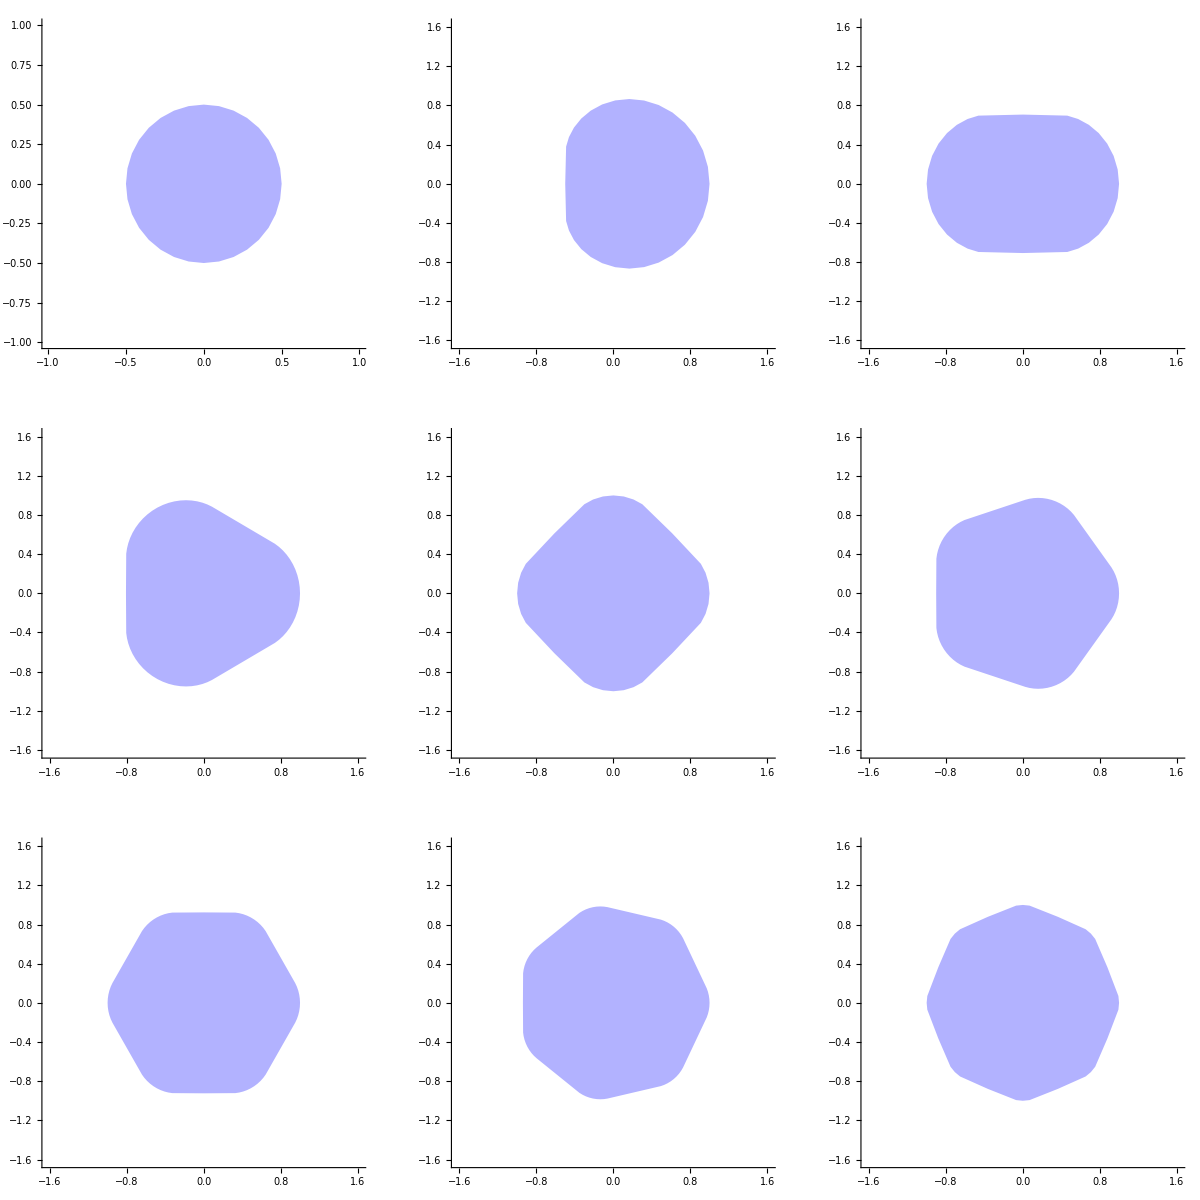

```mathematica
g = GraphicsGrid[Partition[Table[NumericalRangeVisual[A[n]], {n, 2, 10}], 3], ImageSize->Full]
```

```mathematica
Export["nilpotentni.pdf", g]
```

nilpotentni.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["nilpotentni.png"]]]
```

```mathematica
B[n_] := SparseArray[{Band[{1, 2}]->1, {n, 1}->1}, {n, n}];
```

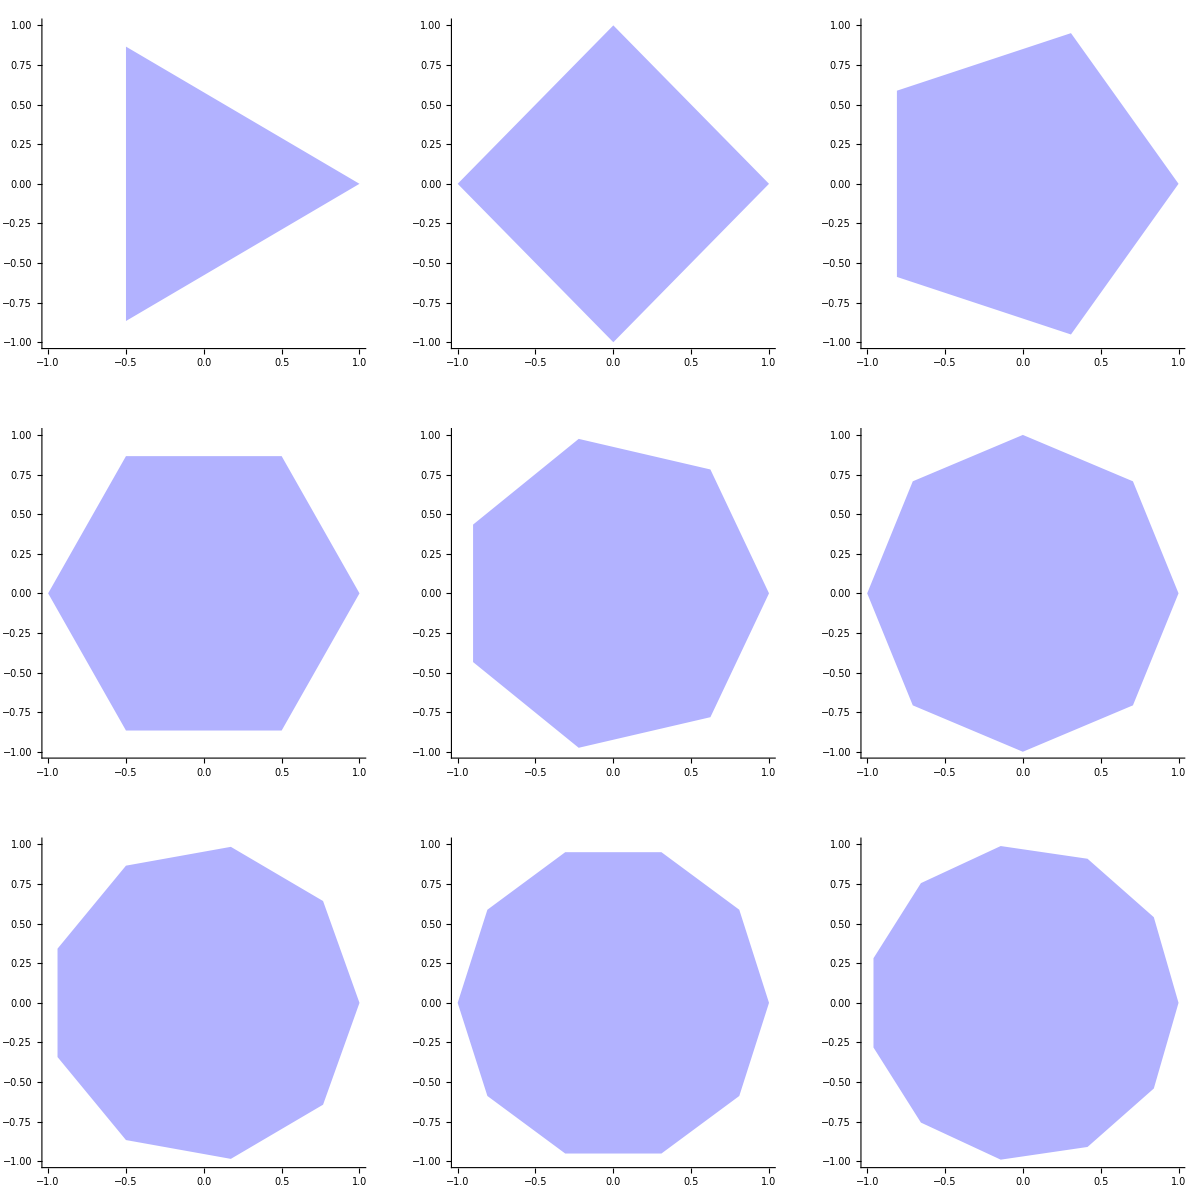

```mathematica
g = GraphicsGrid[Partition[Table[NumericalRangeVisual[B[n]], {n, 3, 11}], 3], ImageSize->Full]
```

```mathematica
F[n_]:=DirectSum[{{0, 2}, {0, 0}},DiagonalMatrix[Table[1.1*Exp[k*I*2π/(n-2)], {k, 0, n-3}]]];
```

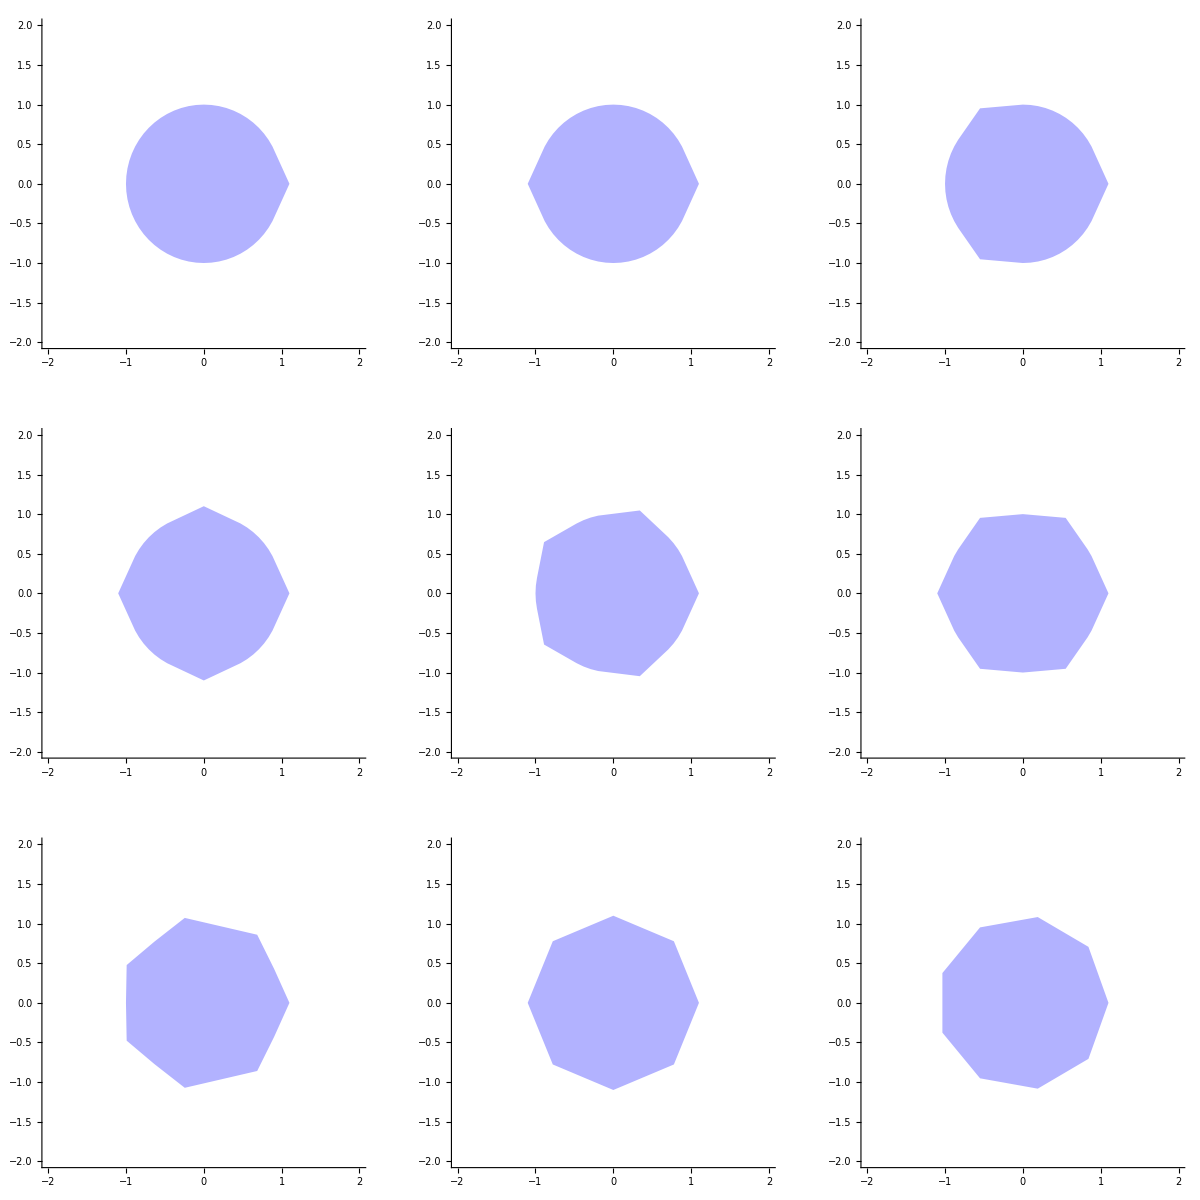

```mathematica
g = GraphicsGrid[Partition[Table[NumericalRangeVisual[F[n]], {n, 3, 11}], 3], ImageSize->Full]
```

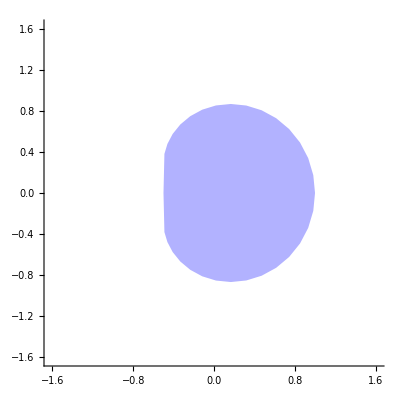

```mathematica
NumericalRangeVisual[{
{0, 1, 1},
{0, 0, 1},
{0, 0, 0}
}]
```

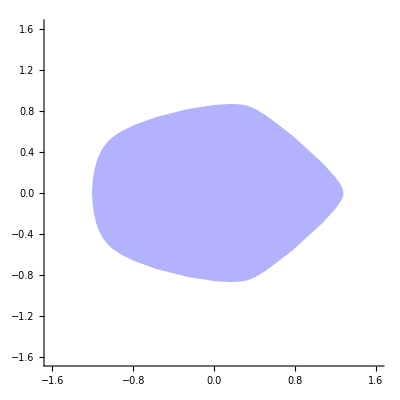

```mathematica
NumericalRangeVisual[
{
{0, 1, 0, 0, 1},
{0, 0, 1, 0, 0},
{0, 0, 0, 1, 0},
{0, 0, 0, 0, 1},
{1, 0, 0, 0, 0}
}
]
```

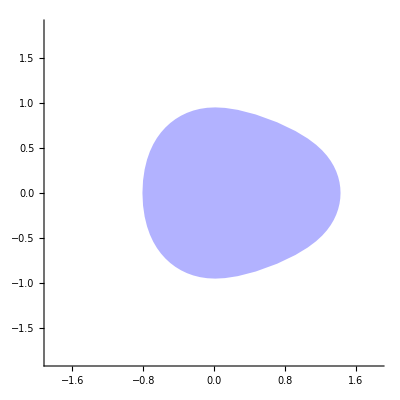

```mathematica
NumericalRangeVisual[
{
{0, 1, 0, 0, 1},
{0, 0, 1, 0, 0},
{0, 0, 0, 1, 0},
{0, 0, 0, 0, 1},
{0, 0, 0, 0, 1}
}
]
```

Stochastic matrices

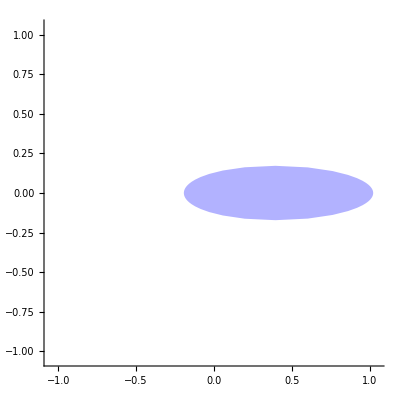

```mathematica
NumericalRangeVisual[{
{1/2, 1/2, 0},
{1/3, 1/3, 1/3},
{1/4, 1/2, 1/4}
}]
```

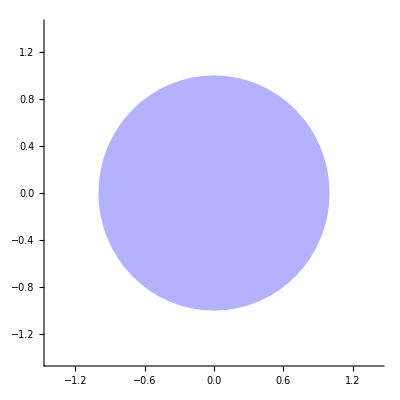

```mathematica
NumericalRangeVisual[
{
{0, Sqrt[2], 0, 0, 0},
{0, 0, 1, 0, 0},
{0, 0, 0, 1, 0},
{0, 0, 0, 0, Sqrt[2]},
{0, 0, 0, 0, 0}
}
]
```

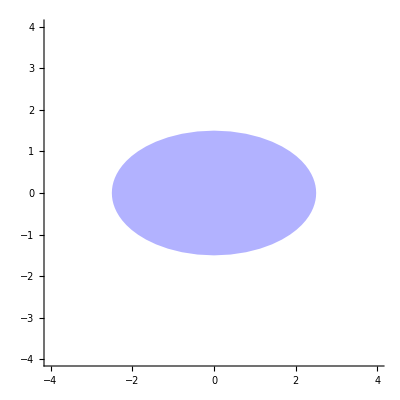

```mathematica
NumericalRangeVisual[{
{0, 1},
{4, 0}
}]
```